Kukulin, Theory of Resonances, ch.6.1.1 Eq.(1.1) ff      S_l(k)=Numerator/(k^(2l+1)cotδ_l-ik^(2l+1))      →_(k→0)        Numerator/(-a_l^-1+1/2 r_l k^2+O(k^4)-ik^(2l+1))
Pade (typeII): X_l(k^2)=(P_N^(l)(k^2))/(Q_M^(l)(k^2))=(p_0+p_1 z+p_2 z^2+p_3 z^3+…)/(1+q_1 z+q_2 z^2+q_3 z^3+…):=k^(2l+1)cotδ_l=-1/a_l+1/2 r_l k^2-1/4 P_l k^4+…  

⇒   S_l(k)=(P_N^(l)(k^2) + ik^(2l+1)Q_M^(l)(k^2))/(P_N^(l)(k^2) - ik^(2l+1)Q_M^(l)(k^2))    ⇒     P_N^(l)(k_res^2)-ik_res^(2l+1)Q_M^(l)(k_res^2)=0

```mathematica
modelX
```

(pp^2 cn[1]+cn[2])/(1+pp^2 cm[1]+pp^4 cm[2])

```mathematica
hbar=197.327053;
Mm=938.92;
m1=3 Mm;m2=Mm;
μ=m1 m2/(m1+m2);
mh2=(2 μ)/(hbar)^2;
```

```mathematica
dataS=Transpose[Import["/home/kirscher/kette_repo/31_resonances/data/tmpS.dat","Data"][[2;;]][[All,3;;]]];
dataP=Transpose[Import["/home/kirscher/kette_repo/31_resonances/data/tmpP.dat","Data"][[2;;]][[All,3;;]]];
dataL=Import["/home/kirscher/kette_repo/31_resonances/data/tmpP.dat","Data"][[1]][[8;;]];
dataMomFM=Import["/home/kirscher/kette_repo/31_resonances/data/tmpP.dat","Data"][[All,1]][[2;;]];
ErangeMeV=dataMomFM^2/mh2;
```

λ = 0.25   : P_pole = {{pp→-2.1763-0.0675485 ⅈ},{pp→-1.03804+0.299621 ⅈ},{pp→-0.125934-0.33828 ⅈ},{pp→0.+0.212415 ⅈ},{pp→0.125934-0.33828 ⅈ},{pp→1.03804+0.299621 ⅈ},{pp→2.1763-0.0675485 ⅈ}}

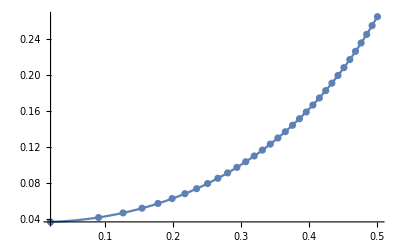

λ = 1   : P_pole = {{pp→-1.31058-0.229114 ⅈ},{pp→-0.911567+0.506278 ⅈ},{pp→-0.139988-0.413521 ⅈ},{pp→0.+0.272716 ⅈ},{pp→0.139988-0.413521 ⅈ},{pp→0.911567+0.506278 ⅈ},{pp→1.31058-0.229114 ⅈ}}

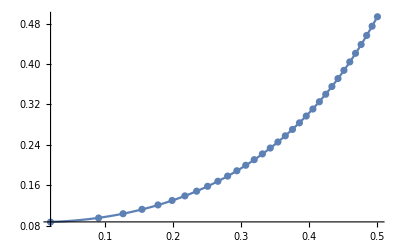

λ = 2.25   : P_pole = {{pp→-1.09297-0.238712 ⅈ},{pp→-0.777028+0.5191 ⅈ},{pp→-0.134134-0.424075 ⅈ},{pp→0.+0.287374 ⅈ},{pp→0.134134-0.424075 ⅈ},{pp→0.777028+0.5191 ⅈ},{pp→1.09297-0.238712 ⅈ}}

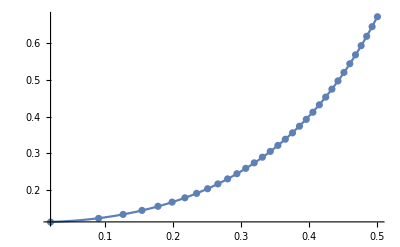

λ = 4   : P_pole = {{pp→-1.06785-0.237181 ⅈ},{pp→-0.753269+0.525968 ⅈ},{pp→-0.131606-0.438883 ⅈ},{pp→0.+0.30019 ⅈ},{pp→0.131606-0.438883 ⅈ},{pp→0.753269+0.525968 ⅈ},{pp→1.06785-0.237181 ⅈ}}

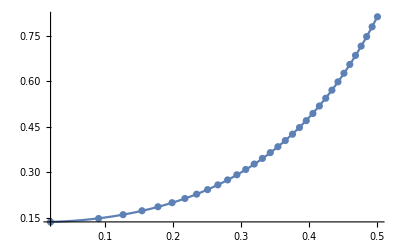

λ = 9   : P_pole = {{pp→-0.900426-0.210559 ⅈ},{pp→-0.622867+0.481379 ⅈ},{pp→-0.0184305-0.39683 ⅈ},{pp→0.+0.252019 ⅈ},{pp→0.0184305-0.39683 ⅈ},{pp→0.622867+0.481379 ⅈ},{pp→0.900426-0.210559 ⅈ}}

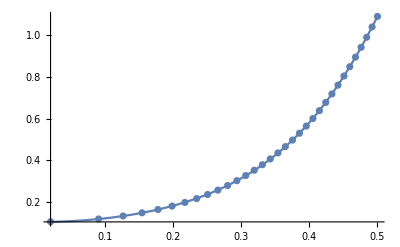

λ = 16   : P_pole = {{pp→-0.898641-0.20791 ⅈ},{pp→-0.61693+0.481157 ⅈ},{pp→0.+0.254526 ⅈ},{pp→0.-0.376116 ⅈ},{pp→0.-0.424903 ⅈ},{pp→0.61693+0.481157 ⅈ},{pp→0.898641-0.20791 ⅈ}}

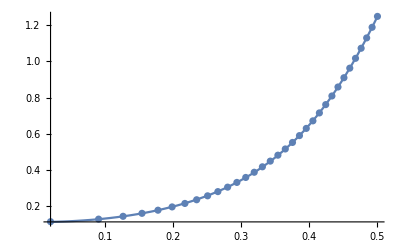

λ = 25   : P_pole = {{pp→-0.901461-0.214948 ⅈ},{pp→-0.610391+0.504309 ⅈ},{pp→0.+0.229456 ⅈ},{pp→0.-0.279812 ⅈ},{pp→0.-0.528367 ⅈ},{pp→0.610391+0.504309 ⅈ},{pp→0.901461-0.214948 ⅈ}}

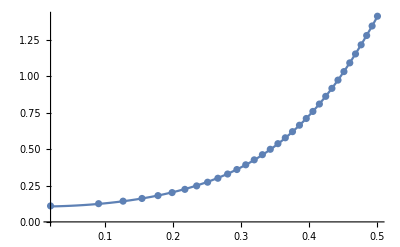

```mathematica
Poles={};PadeSolus={};Lrel=1;

PadeOrderN=1;PadeOrderM=2;

Do[

data=Transpose[{dataMomFM,dataP[[nL]]}];

Clear[coffs];
coffs={Array[cn,PadeOrderN+1],Array[cm,PadeOrderM]};
(*coffs={Table[coffs[[1]][[i]],{i,2,PadeOrderM,2}],Table[coffs[[2]][[i]],{i,2,PadeOrderN,2}]};*)
inicoffs=Transpose[{Flatten[coffs],RandomReal[{-0.01,1.2},Length[Flatten[coffs]]]}];
constr=10^1>#>-10^1&/@Flatten[coffs];
Union[constr,{}];

PadePolyP=coffs[[1]][[PadeOrderN+1]]+Sum[coffs[[1]][[i]] pp^(2 i),{i,1,PadeOrderN,1}];
PadePolyQ=1+Sum[coffs[[2]][[i]] pp^(2 i),{i,1,PadeOrderM,1}];
modelX=PadePolyP/PadePolyQ;

efitmax=Position[Table[If[data[[nn]][[2]]<data[[nn+1]][[2]],data[[nn]][[2]],"42"],{nn,Range[Length[data]-1]}],"42"];
If[efitmax=={},efitmax=Length[data],efitmax=Flatten[efitmax][[1]]];
fitdata=data[[;;efitmax]];

solu=FindFit[fitdata,{modelX,constr},Flatten[coffs],pp,MaxIterations->500];
poles=Solve[((PadePolyP/PadePolyQ-I pp^(2 Lrel+1))/.solu)==0,pp,Complexes];

Print["λ = ",dataL[[nL]],"   : P_pole = ",poles];

Show[Plot[modelX/.solu,{pp,dataMomFM[[1]],dataMomFM[[-1]]}],ListPlot[data]]//Print;

AppendTo[Poles,Transpose[{Table[dataL[[nL]],Length[poles]],Flatten[pp/.poles]}]];

,{nL,Range[Length[dataL]]}]
```

```mathematica
Poland=Transpose[{Flatten[Poles,1][[All,1]],Flatten[Poles,1][[All,2]]}];
PolandRe=Re[Poland];
PolandIm=Transpose[{Flatten[Poles,1][[All,1]],Im[Flatten[Poles,1][[All,2]]]}];
cplxpoles=Transpose[{Re[Poland[[All,2]]],Im[Poland[[All,2]]]}];
Grid[{{
ListPlot[PolandRe,AxesLabel->{"λ [fm^-2]","Re[p_pole] [fm^-1]"},ImageSize->500,PlotRange->Automatic],
ListPlot[PolandIm,AxesLabel->{"λ [fm^-2]","Im[p_pole] [fm^-1]"},ImageSize->500,PlotRange->Automatic],
ListPlot[cplxpoles->Poland[[All,1]],PlotRange->{{0,Automatic},{0,Automatic}},AxesLabel->{"Re[p_pole] [fm^-1]","Im[p_pole] [fm^-1]"},ImageSize->500]
}}]
```

-Graphics-